Henry Osei

```mathematica
visualMVT[f_,a_,b_]:=DynamicModule[{x,g,ξ,p1,p2},
g[x_]=f[x];
Manipulate[
p1=Plot[
{g[x],g[a]+(g[b]-g[a])/(b-a)*(x-a)},
{x,a,b},PlotStyle->{Black,Red}];
p2=Plot[g[ξ]+g'[ξ]*(x-ξ),{x,a,b},PlotStyle->Blue];
Show[p1,p2],{ξ,a,b}]]
```

Syntax::tsntxi: "visualMVT[x^2*Exp[-x/2]] _, -0.5 _, 3  _ := DynamicModule[{x, g, ξ, p1, p2}, g[x_] = f[x]; Manipulate[«1», {ξ, a, b}]]" is incomplete; more input is needed."<>"

```mathematica
f[x_]:=(x^2)*Exp[-x/2]
visualMVT[f, -0.5, 3]
```

```mathematica
Clear f[x_]
f[x_]:=(x+1)/(x-1)
visualMVT[f, 2, 3]
```

Clear ⅇ^(-x_/2) x_^2

```mathematica
Clear[a,b,m,f]
f[x_]:=x^2*Exp[-x/2]
a=-0.5;b=3;
m=(f[b]-f[a])/(b-a)
```

```mathematica
0.4820471677611236
FindRoot[f'[x]==m,{x,0.4820471677611236}]
```

0.482047

{x→0.303568}

```mathematica
Clear[a,b,m,f]
f[x_]:=(x+1)/(x-1)
a=2;b=3;
m=(f[b]-f[a])/(b-a)
```

-1

```mathematica
FindRoot[f'[x]==m,{x,-1}]
```

{x→-0.414214}

```mathematica
Clear[f]
f[x_] := 1/(x-1)^2
Plot[f[x], {x, 1, 3}]
```

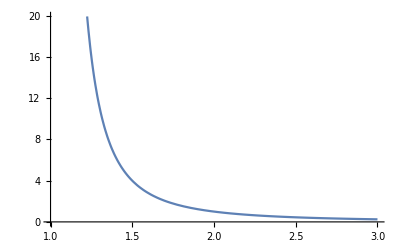

The problem arises because of the discontinuity of y=f(x) at x=3.  Of course the fact that fis not differentiable at x=3 is the reason the Mean Value Theorem fails to apply.

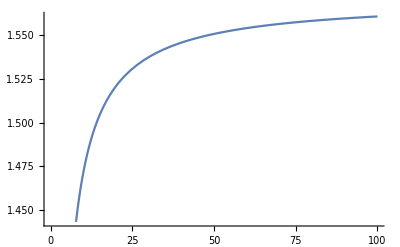

```mathematica
Clear[f]
f[x_] :=ArcTan[x]
Plot[f[x], {x, 0, 100}]
```

```mathematica
The problem arises because of the fact of y=f(x) is unbound at x=infitnity. Of course the fact that f is not a open interval at x=infinity is the reason the Mean Value Theorem fails to apply.
```

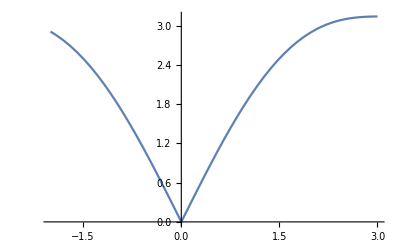

```mathematica
Clear[f]
f[x_] :=Abs[x+Sin[x]]
Plot[f[x], {x, -2, 3}]
```

The problem arises because of the non diffrentiability at x=-2 in the absolute value function. Of course the fact that f is not a closed interval at x=2 is the reason the Mean Value Theorem fails to apply.

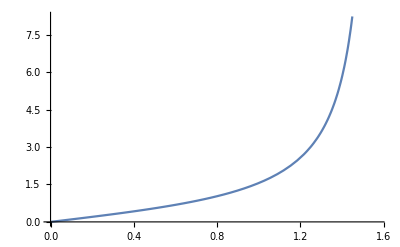

```mathematica
Clear[f]
f[x_] :=Tan[x]
Plot[f[x], {x, 0, Pi/2}]
```

The problem arises because of the fact that [a,b] is unbounded at x=pi. Of course the fact that f is discontinuous interval at x=Pi is the reason the Mean Value Theorem fails to apply

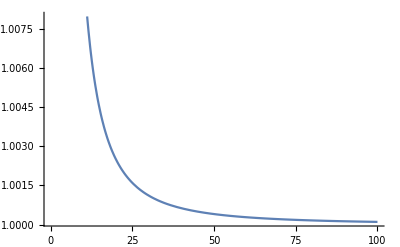

```mathematica
Clear[f]
f[x_] :=1/(x^2)+1
Plot[f[x], {x, 0, 100}]
```

The problem arises because of the fact of y=f(x) is unbound at x=infitnity. Of course the fact that f is not a open interval at x=infinity is the reason the Mean Value Theorem fails to apply.

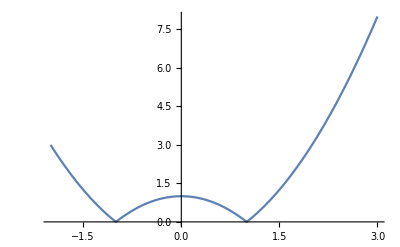

```mathematica
Clear[f]
f[x_] :=Abs[(x^2)-1]
Plot[f[x], {x, -2, 3}]
```

The problem arises because of the discontinuity of y=f(x) at x=3, x=2.  Of course the fact that fis not differentiable at x=3, x=2 is the reason the Mean Value Theorem fails to apply.